## Attempt 1

File is from 
[fphysics@facet-srv01 ~/nate]$ pwd
/home/fphysics/nate

```mathematica
raw = Import["/Users/nmajik/Downloads/bowtiedata_LI11_LI18_repeat.mat","IndeterminateValues"->0];
```

Looking at this by hand, find a chunk which looks worthwhile to expand further

```mathematica
data = Flatten[raw[[6]]];
data = StringSplit/@data;
data[[1]]

data =<|
"ele"->#[[6]],
"axis"->#[[7]],
"offset"->ToExpression[#[[10]]],
"error"->ToExpression[#[[12]]]
|>&/@data;

data[[1]]

data = SortBy[data,#ele&];
```

{02/23/2014,10:42,bowtie_gui,Bowtie,BBA,LI11:BPMS:401,X,Measured,offset:,-1.1191,+/-,0.0054,mm}

<|ele→LI11:BPMS:401,axis→X,offset→-1.1191,error→0.0054|>

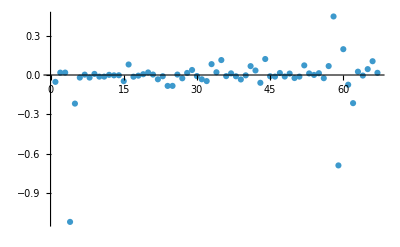

```mathematica
ListPlot[
Select[data,#axis=="X"&][[All,"offset"]],
PlotRange->All
]
```

Hmmm, no... that doesn’t look like the desired plot:
-Graphics-
From http://physics-elog.slac.stanford.edu/facetelog/show.jsp?dir=/2014/09/25.02&pos=2014-02-25T20:30:01

I’m thinking I need to find “ballistic” rather than “bowtie” data

## Attempt 2

```mathematica
raw = Import["/Users/nmajik/Downloads/for_fjd.mat","IndeterminateValues"->0];
```

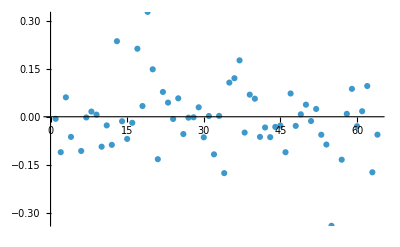

```mathematica
ListPlot[raw[[1,1]]]
```

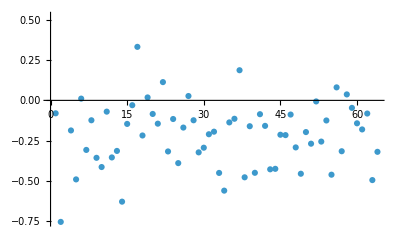

```mathematica
ListPlot[raw[[2,1]]]
```

Also no

## Attempt 3

Fuck it. I hate archeology

Using https://plotdigitizer.com/app

### X

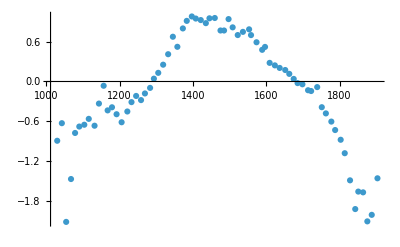

```mathematica
raw = Import["/Users/nmajik/Downloads/plot-data.csv"][[2;;]];

ListPlot[raw]
```

Z values from Bmad

```mathematica
quadZValues = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/quadZValues.json"]//Association
```

<|QM10771→1018.33,QM10781→1018.74,QA11132→1022.05,Q11201→1028.31,QA11265→1034.39,Q11301→1037.63,QM11312→1039.21,QM11358→1046.52,QM11362→1047.17,QM11393→1052.09,Q11401→1053.01,Q11501→1065.35,Q11601→1077.69,Q11701→1090.04,Q11801→1102.38,Q11901→1115.05,Q12201→1129.92,Q12301→1142.26,Q12401→1154.61,Q12501→1166.95,Q12601→1179.29,Q12701→1191.64,Q12801→1203.98,Q12901→1216.65,Q13201→1231.52,Q13301→1243.86,Q13401→1256.21,Q13501→1268.55,Q13601→1280.89,Q13701→1293.24,Q13801→1305.58,Q13901→1318.25,Q14201→1333.12,Q14301→1345.46,Q14401→1357.81,Q14501→1370.15,Q14601→1382.49,Q14701→1394.84,QM14715→1396.88,QM14891→1421.41,Q14901→1421.82,Q15201→1434.72,Q15301→1447.06,Q15401→1459.41,Q15501→1471.75,Q15601→1484.09,Q15701→1496.44,Q15801→1508.78,Q15901→1521.45,Q16201→1536.32,Q16301→1548.66,Q16401→1561.01,Q16501→1573.35,Q16601→1585.69,Q16701→1598.04,Q16801→1610.38,Q16901→1623.05,Q17201→1637.92,Q17301→1650.26,Q17401→1662.61,Q17501→1674.95,Q17601→1687.29,Q17701→1699.64,Q17801→1711.98,Q17901→1724.65,Q18201→1739.52,Q18301→1751.86,Q18401→1764.21,Q18501→1776.55,Q18601→1788.89,Q18701→1801.24,Q18801→1813.58,Q18901→1826.25,Q19201→1841.12,Q19301→1853.46,Q19401→1865.81,Q19501→1878.15,Q19601→1890.49,Q19701→1902.84,Q19801→1915.18,Q19851→1921.57,Q19871→1923.76|>

InterpolatingFunction::dmval: Input value {1018.33} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1018.74} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1022.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

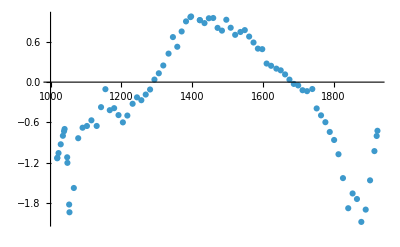

```mathematica
xOffsetInterp = Interpolation[raw,InterpolationOrder->1];

ListPlot[
{
#,
xOffsetInterp[#]
}&/@Values[quadZValues]

]
```

```mathematica
pinkCurveXOffsets =Table[
ele ->xOffsetInterp[quadZValues[ele]] ,
{ele,Keys[quadZValues]}
]//Association;
Export["~/pinkCurveXOffsets.json",pinkCurveXOffsets]
```

InterpolatingFunction::dmval: Input value {1018.33} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1018.74} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1022.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

~/pinkCurveXOffsets.json

### Y

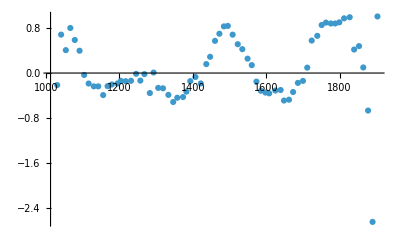

```mathematica
raw = Import["/Users/nmajik/Downloads/plot-data (1).csv"][[2;;]];

ListPlot[raw]
```

InterpolatingFunction::dmval: Input value {1018.33} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1018.74} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1022.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

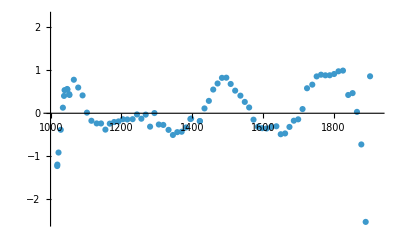

```mathematica
yOffsetInterp = Interpolation[raw,InterpolationOrder->1];

ListPlot[
{
#,
yOffsetInterp[#]
}&/@Values[quadZValues]

]
```

```mathematica
pinkCurveYOffsets =Table[
ele ->yOffsetInterp[quadZValues[ele]] ,
{ele,Keys[quadZValues]}
]//Association;
Export["~/pinkCurveYOffsets.json",pinkCurveYOffsets]
```

InterpolatingFunction::dmval: Input value {1018.33} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1018.74} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1022.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

~/pinkCurveYOffsets.json

## Blue curve

### X

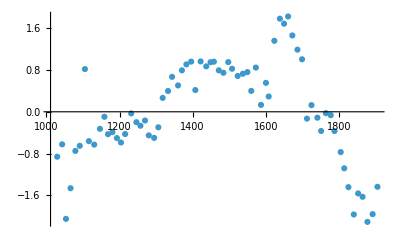

```mathematica
raw = Import["/Users/nmajik/Downloads/plot-data (2).csv"][[2;;]];

ListPlot[raw]
```

InterpolatingFunction::dmval: Input value {1018.33} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1018.74} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1022.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

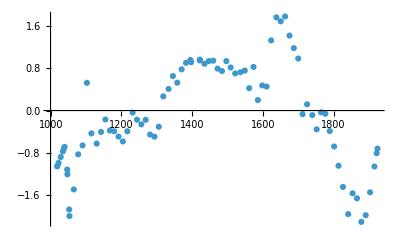

```mathematica
xOffsetInterp = Interpolation[raw,InterpolationOrder->1];

ListPlot[
{
#,
xOffsetInterp[#]
}&/@Values[quadZValues]

]
```

```mathematica
blueCurveXOffsets =Table[
ele ->xOffsetInterp[quadZValues[ele]] ,
{ele,Keys[quadZValues]}
]//Association;
Export["~/blueCurveXOffsets.json",blueCurveXOffsets]
```

InterpolatingFunction::dmval: Input value {1018.33} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1018.74} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1022.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

~/blueCurveXOffsets.json

### Y

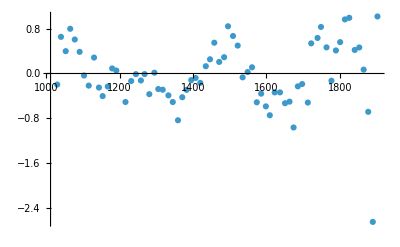

```mathematica
raw = Import["/Users/nmajik/Downloads/plot-data (3).csv"][[2;;]];

ListPlot[raw]
```

InterpolatingFunction::dmval: Input value {1018.33} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1018.74} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1022.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

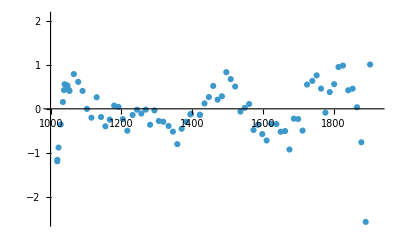

```mathematica
yOffsetInterp = Interpolation[raw,InterpolationOrder->1];

ListPlot[
{
#,
yOffsetInterp[#]
}&/@Values[quadZValues]

]
```

```mathematica
blueCurveYOffsets =Table[
ele ->yOffsetInterp[quadZValues[ele]] ,
{ele,Keys[quadZValues]}
]//Association;
Export["~/blueCurveYOffsets.json",blueCurveYOffsets]
```

InterpolatingFunction::dmval: Input value {1018.33} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1018.74} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1022.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

~/blueCurveYOffsets.json

## Validate

{QM10771→-1.13282,QM10781→-1.12437,QA11132→-1.05529,Q11201→-0.924699,QA11265→-0.797833,Q11301→-0.730221,QM11312→-0.697219,QM11358→-1.11791,QM11362→-1.20052,QM11393→-1.82052,Q11401→-1.9357,Q11501→-1.57434,Q11601→-0.834247,Q11701→-0.677923,Q11801→-0.652289,Q11901→-0.568076,Q12201→-0.65205,Q12301→-0.372296,Q12401→-0.105053,Q12501→-0.417275,Q12601→-0.387348,Q12701→-0.490415,Q12801→-0.598593,Q12901→-0.497148,Q13201→-0.322032,Q13301→-0.2265,Q13401→-0.268878,Q13501→-0.184788,Q13601→-0.10959,Q13701→0.0381969,Q13801→0.131431,Q13901→0.24751,Q14201→0.424006,Q14301→0.669909,Q14401→0.525919,Q14501→0.753548,Q14601→0.903314,Q14701→0.966756,QM14715→0.976595,QM14891→0.922314,Q14901→0.920941,Q15201→0.877772,Q15301→0.949703,Q15401→0.953614,Q15501→0.806686,Q15601→0.765932,Q15701→0.92773,Q15801→0.808852,Q15901→0.70331,Q16201→0.745621,Q16301→0.773542,Q16401→0.677784,Q16501→0.589214,Q16601→0.498256,Q16701→0.49023,Q16801→0.276359,Q16901→0.242908,Q17201→0.20062,Q17301→0.175217,Q17401→0.114782,Q17501→0.0372511,Q17601→-0.026709,Q17701→-0.0488956,Q17801→-0.120572,Q17901→-0.134423,Q18201→-0.102808,Q18301→-0.391214,Q18401→-0.494206,Q18501→-0.595883,Q18601→-0.741072,Q18701→-0.860364,Q18801→-1.07253,Q18901→-1.42759,Q19201→-1.87541,Q19301→-1.65595,Q19401→-1.73835,Q19501→-2.07877,Q19601→-1.89585,Q19701→-1.46085,Q19801→-1.02584,Q19851→-0.80087,Q19871→-0.723573}

{QM10771→-1.05631,QM10781→-1.04916,QA11132→-0.990714,Q11201→-0.880219,QA11265→-0.772878,Q11301→-0.715671,QM11312→-0.687749,QM11358→-1.11707,QM11362→-1.20588,QM11393→-1.87238,Q11401→-1.99619,Q11501→-1.49244,Q11601→-0.82853,Q11701→-0.659664,Q11801→0.523919,Q11901→-0.432407,Q12201→-0.625431,Q12301→-0.40425,Q12401→-0.169328,Q12501→-0.378084,Q12601→-0.392043,Q12701→-0.492363,Q12801→-0.585228,Q12901→-0.39174,Q13201→-0.038607,Q13301→-0.173104,Q13401→-0.261241,Q13501→-0.175372,Q13601→-0.454114,Q13701→-0.494878,Q13801→-0.306174,Q13901→0.268655,Q14201→0.408939,Q14301→0.65179,Q14401→0.527133,Q14501→0.778525,Q14601→0.903609,Q14701→0.955948,QM14715→0.915647,QM14891→0.948225,Q14901→0.963756,Q15201→0.885198,Q15301→0.93621,Q15401→0.943569,Q15501→0.792653,Q15601→0.747135,Q15701→0.935961,Q15801→0.814721,Q15901→0.701887,Q16201→0.724666,Q16301→0.757269,Q16401→0.424201,Q16501→0.824965,Q16601→0.197614,Q16701→0.475024,Q16801→0.453947,Q16901→1.32742,Q17201→1.76248,Q17301→1.68816,Q17401→1.78008,Q17501→1.41824,Q17601→1.18105,Q17701→0.984253,Q17801→-0.0675824,Q17901→0.11786,Q18201→-0.0863019,Q18301→-0.355845,Q18401→-0.0339174,Q18501→-0.061141,Q18601→-0.38774,Q18701→-0.679881,Q18801→-1.04454,Q18901→-1.44518,Q19201→-1.95948,Q19301→-1.56641,Q19401→-1.65986,Q19501→-2.10676,Q19601→-1.97936,Q19701→-1.54721,Q19801→-1.05921,Q19851→-0.806832,Q19871→-0.720119}

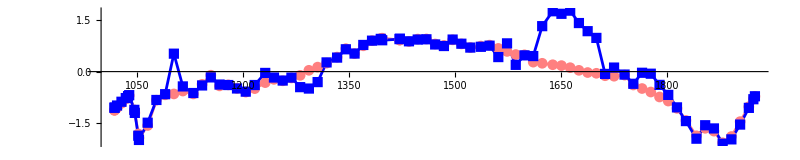

```mathematica
importedPinkX = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/pinkCurveXOffsets.json"]
importedBlueX = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/blueCurveXOffsets.json"]

ListPlot[
{
Transpose[{
quadZValues[#]&/@Keys[importedPinkX],
Values[importedPinkX]
}],
Transpose[{
quadZValues[#]&/@Keys[importedBlueX],
Values[importedBlueX]
}]
},
PlotStyle->{Pink,Blue},
Joined->True,
PlotMarkers->Automatic,
ImageSize->800,
AspectRatio->0.2
]
```

{QM10771→-1.22556,QM10781→-1.19137,QA11132→-0.911946,Q11201→-0.383685,QA11265→0.129498,Q11301→0.402996,QM11312→0.536491,QM11358→0.563397,QM11362→0.549344,QM11393→0.443876,Q11401→0.424283,Q11501→0.777984,Q11601→0.596889,Q11701→0.4144,Q11801→0.0143311,Q11901→-0.174404,Q12201→-0.236015,Q12301→-0.236948,Q12401→-0.37987,Q12501→-0.241259,Q12601→-0.203294,Q12701→-0.18933,Q12801→-0.139162,Q12901→-0.144342,Q13201→-0.137597,Q13301→-0.0279045,Q13401→-0.126729,Q13501→-0.0319557,Q13601→-0.311072,Q13701→0.00459292,Q13801→-0.261359,Q13901→-0.271059,Q14201→-0.385828,Q14301→-0.504599,Q14401→-0.438581,Q14501→-0.428872,Q14601→-0.330018,Q14701→-0.133958,QM14715→-0.123452,QM14891→-0.182815,Q14901→-0.182664,Q15201→0.11214,Q15301→0.287102,Q15401→0.550141,Q15501→0.690926,Q15601→0.821718,Q15701→0.825522,Q15801→0.679579,Q15901→0.525148,Q16201→0.408496,Q16301→0.263141,Q16401→0.134077,Q16501→-0.149145,Q16601→-0.315542,Q16701→-0.346456,Q16801→-0.354301,Q16901→-0.316924,Q17201→-0.302454,Q17301→-0.486913,Q17401→-0.468772,Q17501→-0.317617,Q17601→-0.172876,Q17701→-0.141143,Q17801→0.0973181,Q17901→0.580334,Q18201→0.664073,Q18301→0.855216,Q18401→0.894858,Q18501→0.8806,Q18601→0.88188,Q18701→0.911158,Q18801→0.973733,Q18901→0.990167,Q19201→0.423996,Q19301→0.46759,Q19401→0.032077,Q19501→-0.724365,Q19601→-2.52227,Q19701→0.85817,Q19801→4.23861,Q19851→5.98686,Q19871→6.58754}

{QM10771→-1.18859,QM10781→-1.1547,QA11132→-0.877756,Q11201→-0.354177,QA11265→0.154457,Q11301→0.425531,QM11312→0.557843,QM11358→0.531927,QM11362→0.519125,QM11393→0.423051,Q11401→0.405203,Q11501→0.787416,Q11601→0.61009,Q11701→0.40599,Q11801→-0.00241392,Q11901→-0.201035,Q12201→0.261887,Q12301→-0.186715,Q12401→-0.395879,Q12501→-0.24453,Q12601→0.0743926,Q12701→0.045201,Q12801→-0.232961,Q12901→-0.496501,Q13201→-0.138896,Q13301→-0.0194274,Q13401→-0.107277,Q13501→-0.0184211,Q13601→-0.361108,Q13701→-0.0359203,Q13801→-0.276073,Q13901→-0.292403,Q14201→-0.38914,Q14301→-0.517631,Q14401→-0.800333,Q14501→-0.451751,Q14601→-0.294189,Q14701→-0.126503,QM14715→-0.113132,QM14891→-0.140162,Q14901→-0.132088,Q15201→0.121849,Q15301→0.266508,Q15401→0.51882,Q15501→0.207242,Q15601→0.284162,Q15701→0.830599,Q15801→0.673263,Q15901→0.504937,Q16201→-0.0624588,Q16301→0.0226868,Q16401→0.110209,Q16501→-0.479156,Q16601→-0.36182,Q16701→-0.572106,Q16801→-0.717427,Q16901→-0.336524,Q17201→-0.344995,Q17301→-0.518612,Q17401→-0.502926,Q17501→-0.921715,Q17601→-0.223904,Q17701→-0.230759,Q17801→-0.493274,Q17901→0.54973,Q18201→0.632253,Q18301→0.758167,Q18401→0.457936,Q18501→-0.08658,Q18601→0.378677,Q18701→0.558548,Q18801→0.947112,Q18901→0.980394,Q19201→0.419888,Q19301→0.456952,Q19401→0.0359333,Q19501→-0.757886,Q19601→-2.5623,Q19701→1.00446,Q19801→4.57121,Q19851→6.41581,Q19871→7.04959}

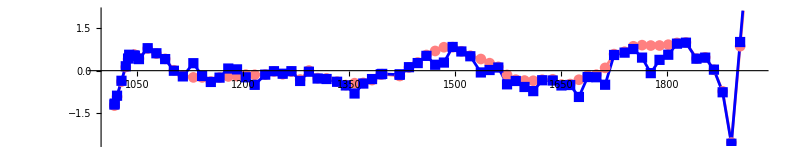

```mathematica
importedPinkY = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/pinkCurveYOffsets.json"]
importedBlueY = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/blueCurveYOffsets.json"]

ListPlot[
{
Transpose[{
quadZValues[#]&/@Keys[importedPinkY],
Values[importedPinkY]
}],
Transpose[{
quadZValues[#]&/@Keys[importedBlueY],
Values[importedBlueY]
}]
},
PlotStyle->{Pink,Blue},
Joined->True,
PlotMarkers->Automatic,
ImageSize->800,
AspectRatio->0.2
]
```